```mathematica
data = Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/initalvext2stage.csv","table"];
```

```mathematica
plotdata=Transpose[{Table[10*10^i,{i,-1,9,0.01}],Flatten[data]}];
```

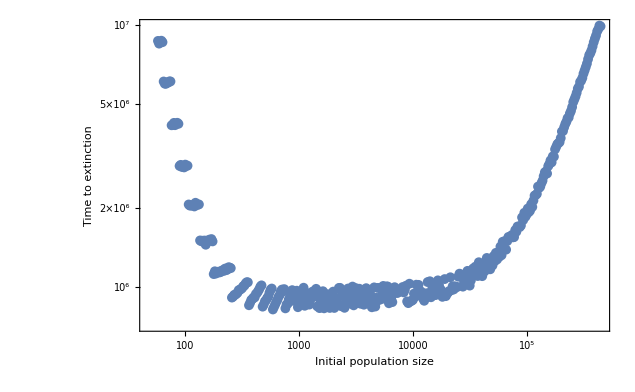

```mathematica
ListLogLogPlot[plotdata,Frame->True,FrameLabel->{"Initial population size","Time to extinction"}]
```

```mathematica
Table[10*10^i,{i,-1,9,0.01}]
```

{1.,1.02329,1.04713,1.07152,1.09648,1.12202,1.14815,1.1749,1.20226,1.23027,1.25893,1.28825,1.31826,1.34896,1.38038,1.41254,1.44544,1.47911,1.51356,1.54882,1.58489,1.62181,1.65959,1.69824,1.7378,1.77828,1.8197,1.86209,1.90546,1.94984,1.99526,2.04174,2.0893,2.13796,2.18776,2.23872,2.29087,2.34423,2.39883,2.45471,2.51189,2.5704,2.63027,2.69153,2.75423,2.81838,2.88403,2.95121,3.01995,3.0903,3.16228,3.23594,3.31131,3.38844,3.46737,3.54813,3.63078,3.71535,3.80189,3.89045,3.98107,4.0738,4.16869,4.2658,4.36516,4.46684,4.57088,4.67735,4.7863,4.89779,5.01187,5.12861,5.24807,5.37032,5.49541,5.62341,5.7544,5.88844,6.0256,6.16595,6.30957,6.45654,6.60693,6.76083,6.91831,7.07946,7.24436,7.4131,7.58578,7.76247,7.94328,8.12831,8.31764,8.51138,8.70964,8.91251,9.12011,9.33254,9.54993,9.77237,10.,10.2329,10.4713,10.7152,10.9648,11.2202,11.4815,11.749,12.0226,12.3027,12.5893,12.8825,13.1826,13.4896,13.8038,14.1254,14.4544,14.7911,15.1356,15.4882,15.8489,16.2181,16.5959,16.9824,17.378,17.7828,18.197,18.6209,19.0546,19.4984,19.9526,20.4174,20.893,21.3796,21.8776,22.3872,22.9087,23.4423,23.9883,24.5471,25.1189,25.704,26.3027,26.9153,27.5423,28.1838,28.8403,29.5121,30.1995,30.903,31.6228,32.3594,33.1131,33.8844,34.6737,35.4813,36.3078,37.1535,38.0189,38.9045,39.8107,40.738,41.6869,42.658,43.6516,44.6684,45.7088,46.7735,47.863,48.9779,50.1187,51.2861,52.4807,53.7032,54.9541,56.2341,57.544,58.8844,60.256,61.6595,63.0957,64.5654,66.0693,67.6083,69.1831,70.7946,72.4436,74.131,75.8578,77.6247,79.4328,81.2831,83.1764,85.1138,87.0964,89.1251,91.2011,93.3254,95.4993,97.7237,100.,102.329,104.713,107.152,109.648,112.202,114.815,117.49,120.226,123.027,125.893,128.825,131.826,134.896,138.038,141.254,144.544,147.911,151.356,154.882,158.489,162.181,165.959,169.824,173.78,177.828,181.97,186.209,190.546,194.984,199.526,204.174,208.93,213.796,218.776,223.872,229.087,234.423,239.883,245.471,251.189,257.04,263.027,269.153,275.423,281.838,288.403,295.121,301.995,309.03,316.228,323.594,331.131,338.844,346.737,354.813,363.078,371.535,380.189,389.045,398.107,407.38,416.869,426.58,436.516,446.684,457.088,467.735,478.63,489.779,501.187,512.861,524.807,537.032,549.541,562.341,575.44,588.844,602.56,616.595,630.957,645.654,660.693,676.083,691.831,707.946,724.436,741.31,758.578,776.247,794.328,812.831,831.764,851.138,870.964,891.251,912.011,933.254,954.993,977.237,1000.,1023.29,1047.13,1071.52,1096.48,1122.02,1148.15,1174.9,1202.26,1230.27,1258.93,1288.25,1318.26,1348.96,1380.38,1412.54,1445.44,1479.11,1513.56,1548.82,1584.89,1621.81,1659.59,1698.24,1737.8,1778.28,1819.7,1862.09,1905.46,1949.84,1995.26,2041.74,2089.3,2137.96,2187.76,2238.72,2290.87,2344.23,2398.83,2454.71,2511.89,2570.4,2630.27,2691.53,2754.23,2818.38,2884.03,2951.21,3019.95,3090.3,3162.28,3235.94,3311.31,3388.44,3467.37,3548.13,3630.78,3715.35,3801.89,3890.45,3981.07,4073.8,4168.69,4265.8,4365.16,4466.84,4570.88,4677.35,4786.3,4897.79,5011.87,5128.61,5248.07,5370.32,5495.41,5623.41,5754.4,5888.44,6025.6,6165.95,6309.57,6456.54,6606.93,6760.83,6918.31,7079.46,7244.36,7413.1,7585.78,7762.47,7943.28,8128.31,8317.64,8511.38,8709.64,8912.51,9120.11,9332.54,9549.93,9772.37,10000.,10232.9,10471.3,10715.2,10964.8,11220.2,11481.5,11749.,12022.6,12302.7,12589.3,12882.5,13182.6,13489.6,13803.8,14125.4,14454.4,14791.1,15135.6,15488.2,15848.9,16218.1,16595.9,16982.4,17378.,17782.8,18197.,18620.9,19054.6,19498.4,19952.6,20417.4,20893.,21379.6,21877.6,22387.2,22908.7,23442.3,23988.3,24547.1,25118.9,25704.,26302.7,26915.3,27542.3,28183.8,28840.3,29512.1,30199.5,30903.,31622.8,32359.4,33113.1,33884.4,34673.7,35481.3,36307.8,37153.5,38018.9,38904.5,39810.7,40738.,41686.9,42658.,43651.6,44668.4,45708.8,46773.5,47863.,48977.9,50118.7,51286.1,52480.7,53703.2,54954.1,56234.1,57544.,58884.4,60256.,61659.5,63095.7,64565.4,66069.3,67608.3,69183.1,70794.6,72443.6,74131.,75857.8,77624.7,79432.8,81283.1,83176.4,85113.8,87096.4,89125.1,91201.1,93325.4,95499.3,97723.7,100000.,102329.,104713.,107152.,109648.,112202.,114815.,117490.,120226.,123027.,125893.,128825.,131826.,134896.,138038.,141254.,144544.,147911.,151356.,154882.,158489.,162181.,165959.,169824.,173780.,177828.,181970.,186209.,190546.,194984.,199526.,204174.,208930.,213796.,218776.,223872.,229087.,234423.,239883.,245471.,251189.,257040.,263027.,269153.,275423.,281838.,288403.,295121.,301995.,309030.,316228.,323594.,331131.,338844.,346737.,354813.,363078.,371535.,380189.,389045.,398107.,407380.,416869.,426580.,436516.,446684.,457088.,467735.,478630.,489779.,501187.,512861.,524807.,537032.,549541.,562341.,575440.,588844.,602560.,616595.,630957.,645654.,660693.,676083.,691831.,707946.,724436.,741310.,758578.,776247.,794328.,812831.,831764.,851138.,870964.,891251.,912011.,933254.,954993.,977237.,1.×10^6,1.02329×10^6,1.04713×10^6,1.07152×10^6,1.09648×10^6,1.12202×10^6,1.14815×10^6,1.1749×10^6,1.20226×10^6,1.23027×10^6,1.25893×10^6,1.28825×10^6,1.31826×10^6,1.34896×10^6,1.38038×10^6,1.41254×10^6,1.44544×10^6,1.47911×10^6,1.51356×10^6,1.54882×10^6,1.58489×10^6,1.62181×10^6,1.65959×10^6,1.69824×10^6,1.7378×10^6,1.77828×10^6,1.8197×10^6,1.86209×10^6,1.90546×10^6,1.94984×10^6,1.99526×10^6,2.04174×10^6,2.0893×10^6,2.13796×10^6,2.18776×10^6,2.23872×10^6,2.29087×10^6,2.34423×10^6,2.39883×10^6,2.45471×10^6,2.51189×10^6,2.5704×10^6,2.63027×10^6,2.69153×10^6,2.75423×10^6,2.81838×10^6,2.88403×10^6,2.95121×10^6,3.01995×10^6,3.0903×10^6,3.16228×10^6,3.23594×10^6,3.31131×10^6,3.38844×10^6,3.46737×10^6,3.54813×10^6,3.63078×10^6,3.71535×10^6,3.80189×10^6,3.89045×10^6,3.98107×10^6,4.0738×10^6,4.16869×10^6,4.2658×10^6,4.36516×10^6,4.46684×10^6,4.57088×10^6,4.67735×10^6,4.7863×10^6,4.89779×10^6,5.01187×10^6,5.12861×10^6,5.24807×10^6,5.37032×10^6,5.49541×10^6,5.62341×10^6,5.7544×10^6,5.88844×10^6,6.0256×10^6,6.16595×10^6,6.30957×10^6,6.45654×10^6,6.60693×10^6,6.76083×10^6,6.91831×10^6,7.07946×10^6,7.24436×10^6,7.4131×10^6,7.58578×10^6,7.76247×10^6,7.94328×10^6,8.12831×10^6,8.31764×10^6,8.51138×10^6,8.70964×10^6,8.91251×10^6,9.12011×10^6,9.33254×10^6,9.54993×10^6,9.77237×10^6,1.×10^7,1.02329×10^7,1.04713×10^7,1.07152×10^7,1.09648×10^7,1.12202×10^7,1.14815×10^7,1.1749×10^7,1.20226×10^7,1.23027×10^7,1.25893×10^7,1.28825×10^7,1.31826×10^7,1.34896×10^7,1.38038×10^7,1.41254×10^7,1.44544×10^7,1.47911×10^7,1.51356×10^7,1.54882×10^7,1.58489×10^7,1.62181×10^7,1.65959×10^7,1.69824×10^7,1.7378×10^7,1.77828×10^7,1.8197×10^7,1.86209×10^7,1.90546×10^7,1.94984×10^7,1.99526×10^7,2.04174×10^7,2.0893×10^7,2.13796×10^7,2.18776×10^7,2.23872×10^7,2.29087×10^7,2.34423×10^7,2.39883×10^7,2.45471×10^7,2.51189×10^7,2.5704×10^7,2.63027×10^7,2.69153×10^7,2.75423×10^7,2.81838×10^7,2.88403×10^7,2.95121×10^7,3.01995×10^7,3.0903×10^7,3.16228×10^7,3.23594×10^7,3.31131×10^7,3.38844×10^7,3.46737×10^7,3.54813×10^7,3.63078×10^7,3.71535×10^7,3.80189×10^7,3.89045×10^7,3.98107×10^7,4.0738×10^7,4.16869×10^7,4.2658×10^7,4.36516×10^7,4.46684×10^7,4.57088×10^7,4.67735×10^7,4.7863×10^7,4.89779×10^7,5.01187×10^7,5.12861×10^7,5.24807×10^7,5.37032×10^7,5.49541×10^7,5.62341×10^7,5.7544×10^7,5.88844×10^7,6.0256×10^7,6.16595×10^7,6.30957×10^7,6.45654×10^7,6.60693×10^7,6.76083×10^7,6.91831×10^7,7.07946×10^7,7.24436×10^7,7.4131×10^7,7.58578×10^7,7.76247×10^7,7.94328×10^7,8.12831×10^7,8.31764×10^7,8.51138×10^7,8.70964×10^7,8.91251×10^7,9.12011×10^7,9.33254×10^7,9.54993×10^7,9.77237×10^7,1.×10^8,1.02329×10^8,1.04713×10^8,1.07152×10^8,1.09648×10^8,1.12202×10^8,1.14815×10^8,1.1749×10^8,1.20226×10^8,1.23027×10^8,1.25893×10^8,1.28825×10^8,1.31826×10^8,1.34896×10^8,1.38038×10^8,1.41254×10^8,1.44544×10^8,1.47911×10^8,1.51356×10^8,1.54882×10^8,1.58489×10^8,1.62181×10^8,1.65959×10^8,1.69824×10^8,1.7378×10^8,1.77828×10^8,1.8197×10^8,1.86209×10^8,1.90546×10^8,1.94984×10^8,1.99526×10^8,2.04174×10^8,2.0893×10^8,2.13796×10^8,2.18776×10^8,2.23872×10^8,2.29087×10^8,2.34423×10^8,2.39883×10^8,2.45471×10^8,2.51189×10^8,2.5704×10^8,2.63027×10^8,2.69153×10^8,2.75423×10^8,2.81838×10^8,2.88403×10^8,2.95121×10^8,3.01995×10^8,3.0903×10^8,3.16228×10^8,3.23594×10^8,3.31131×10^8,3.38844×10^8,3.46737×10^8,3.54813×10^8,3.63078×10^8,3.71535×10^8,3.80189×10^8,3.89045×10^8,3.98107×10^8,4.0738×10^8,4.16869×10^8,4.2658×10^8,4.36516×10^8,4.46684×10^8,4.57088×10^8,4.67735×10^8,4.7863×10^8,4.89779×10^8,5.01187×10^8,5.12861×10^8,5.24807×10^8,5.37032×10^8,5.49541×10^8,5.62341×10^8,5.7544×10^8,5.88844×10^8,6.0256×10^8,6.16595×10^8,6.30957×10^8,6.45654×10^8,6.60693×10^8,6.76083×10^8,6.91831×10^8,7.07946×10^8,7.24436×10^8,7.4131×10^8,7.58578×10^8,7.76247×10^8,7.94328×10^8,8.12831×10^8,8.31764×10^8,8.51138×10^8,8.70964×10^8,8.91251×10^8,9.12011×10^8,9.33254×10^8,9.54993×10^8,9.77237×10^8,1.×10^9,1.02329×10^9,1.04713×10^9,1.07152×10^9,1.09648×10^9,1.12202×10^9,1.14815×10^9,1.1749×10^9,1.20226×10^9,1.23027×10^9,1.25893×10^9,1.28825×10^9,1.31826×10^9,1.34896×10^9,1.38038×10^9,1.41254×10^9,1.44544×10^9,1.47911×10^9,1.51356×10^9,1.54882×10^9,1.58489×10^9,1.62181×10^9,1.65959×10^9,1.69824×10^9,1.7378×10^9,1.77828×10^9,1.8197×10^9,1.86209×10^9,1.90546×10^9,1.94984×10^9,1.99526×10^9,2.04174×10^9,2.0893×10^9,2.13796×10^9,2.18776×10^9,2.23872×10^9,2.29087×10^9,2.34423×10^9,2.39883×10^9,2.45471×10^9,2.51189×10^9,2.5704×10^9,2.63027×10^9,2.69153×10^9,2.75423×10^9,2.81838×10^9,2.88403×10^9,2.95121×10^9,3.01995×10^9,3.0903×10^9,3.16228×10^9,3.23594×10^9,3.31131×10^9,3.38844×10^9,3.46737×10^9,3.54813×10^9,3.63078×10^9,3.71535×10^9,3.80189×10^9,3.89045×10^9,3.98107×10^9,4.0738×10^9,4.16869×10^9,4.2658×10^9,4.36516×10^9,4.46684×10^9,4.57088×10^9,4.67735×10^9,4.7863×10^9,4.89779×10^9,5.01187×10^9,5.12861×10^9,5.24807×10^9,5.37032×10^9,5.49541×10^9,5.62341×10^9,5.7544×10^9,5.88844×10^9,6.0256×10^9,6.16595×10^9,6.30957×10^9,6.45654×10^9,6.60693×10^9,6.76083×10^9,6.91831×10^9,7.07946×10^9,7.24436×10^9,7.4131×10^9,7.58578×10^9,7.76247×10^9,7.94328×10^9,8.12831×10^9,8.31764×10^9,8.51138×10^9,8.70964×10^9,8.91251×10^9,9.12011×10^9,9.33254×10^9,9.54993×10^9,9.77237×10^9,1.×10^10}

```mathematica
Flatten[data]
```

{Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,Inf,8.72058×10^6,8.51519×10^6,8.62072×10^6,8.73638×10^6,8.62471×10^6,6.10052×10^6,5.98383×10^6,5.97747×10^6,6.04541×10^6,6.0435×10^6,6.10461×10^6,6.10364×10^6,4.14843×10^6,4.15788×10^6,4.23689×10^6,4.15161×10^6,4.19939×10^6,4.24044×10^6,4.20184×10^6,2.89932×10^6,2.92743×10^6,2.87411×10^6,2.89799×10^6,2.86215×10^6,2.9338×10^6,2.9041×10^6,2.90585×10^6,2.06527×10^6,2.04512×10^6,2.04648×10^6,2.04912×10^6,2.05125×10^6,2.02928×10^6,2.09654×10^6,2.0619×10^6,2.05976×10^6,2.06638×10^6,1.50447×10^6,1.49443×10^6,1.5011×10^6,1.48419×10^6,1.50348×10^6,1.44868×10^6,1.49361×10^6,1.49665×10^6,1.51462×10^6,1.50223×10^6,1.52293×10^6,1.49198×10^6,1.11869×10^6,1.14665×10^6,1.12421×10^6,1.13872×10^6,1.14232×10^6,1.13472×10^6,1.13894×10^6,1.15304×10^6,1.15712×10^6,1.15061×10^6,1.17439×10^6,1.15918×10^6,1.16368×10^6,1.18798×10^6,1.18528×10^6,1.17888×10^6,909614.,916818.,931116.,932907.,941052.,950120.,971284.,974338.,980613.,988972.,1.00614×10^6,1.01114×10^6,1.02952×10^6,1.04139×10^6,1.04078×10^6,850263.,868359.,890922.,897953.,910715.,910770.,938223.,945700.,961630.,978503.,1.00128×10^6,1.01298×10^6,839805.,855807.,880183.,888287.,905961.,918133.,949384.,974537.,985120.,819154.,837541.,855420.,874926.,892344.,916038.,930906.,961113.,976179.,959947.,979949.,827236.,855794.,861641.,895340.,913775.,942226.,971220.,884209.,904508.,934430.,966480.,835738.,853327.,883371.,919912.,946976.,992201.,846353.,864394.,902948.,944772.,855165.,893777.,938138.,959692.,917092.,946477.,982539.,842421.,960731.,829186.,876873.,914881.,962074.,827504.,853256.,900044.,937150.,876386.,830306.,875089.,917001.,958679.,830199.,866594.,864375.,905824.,990168.,990972.,843167.,936711.,948250.,831157.,873513.,931697.,985081.,863334.,914336.,945291.,1.0022×10^6,849455.,916143.,988500.,866345.,922519.,983377.,861874.,912439.,966403.,854352.,902543.,988160.,875507.,959759.,860862.,929213.,835159.,867058.,995115.,840587.,907915.,990431.,889078.,989785.,896244.,928944.,1.00791×10^6,902246.,982032.,1.00351×10^6,1.00252×10^6,865260.,961771.,899117.,874165.,943141.,996640.,968989.,947051.,950010.,968577.,975811.,984307.,998062.,952154.,975187.,1.00989×10^6,879531.,866221.,1.02789×10^6,879482.,885266.,890383.,941833.,915570.,1.01893×10^6,952592.,1.01757×10^6,951856.,961051.,948182.,901807.,884277.,915483.,945013.,1.04286×10^6,917406.,1.05027×10^6,912310.,981846.,986539.,962845.,929706.,999139.,1.05865×10^6,1.01539×10^6,981607.,969622.,915572.,938871.,1.07066×10^6,921140.,940220.,951652.,964018.,1.08775×10^6,970893.,1.0051×10^6,977273.,1.00485×10^6,996632.,998835.,1.09308×10^6,1.12295×10^6,1.11557×10^6,1.10549×10^6,1.00151×10^6,1.04525×10^6,1.10888×10^6,1.04445×10^6,1.15088×10^6,1.08361×10^6,1.01068×10^6,1.05697×10^6,1.14235×10^6,1.1757×10^6,1.15188×10^6,1.19432×10^6,1.12485×10^6,1.09985×10^6,1.2418×10^6,1.19373×10^6,1.14606×10^6,1.09851×10^6,1.22321×10^6,1.14471×10^6,1.20875×10^6,1.28962×10^6,1.18786×10^6,1.17865×10^6,1.16687×10^6,1.21388×10^6,1.20656×10^6,1.31021×10^6,1.25348×10^6,1.34886×10^6,1.27188×10^6,1.31777×10^6,1.3023×10^6,1.42522×10^6,1.32158×10^6,1.48729×10^6,1.46228×10^6,1.49776×10^6,1.38757×10^6,1.49592×10^6,1.55177×10^6,1.54266×10^6,1.55629×10^6,1.57758×10^6,1.54595×10^6,1.54943×10^6,1.64736×10^6,1.62448×10^6,1.70096×10^6,1.69995×10^6,1.69266×10^6,1.71567×10^6,1.84298×10^6,1.80015×10^6,1.9201×10^6,1.85427×10^6,1.89211×10^6,1.99265×10^6,1.93074×10^6,1.95465×10^6,2.06982×10^6,2.02036×10^6,2.13728×10^6,2.23317×10^6,2.2435×10^6,2.26624×10^6,2.41796×10^6,2.3882×10^6,2.41553×10^6,2.4892×10^6,2.54663×10^6,2.65028×10^6,2.74157×10^6,2.76344×10^6,2.71232×10^6,2.89458×10^6,2.94992×10^6,3.04464×10^6,2.99269×10^6,3.1548×10^6,3.14612×10^6,3.35573×10^6,3.43013×10^6,3.51234×10^6,3.54664×10^6,3.57633×10^6,3.70579×10^6,3.92706×10^6,3.94159×10^6,4.0774×10^6,4.1945×10^6,4.28232×10^6,4.41756×10^6,4.44311×10^6,4.60301×10^6,4.70744×10^6,4.86853×10^6,5.09012×10^6,5.21373×10^6,5.34936×10^6,5.52148×10^6,5.73288×10^6,5.82596×10^6,6.07542×10^6,6.14758×10^6,6.29572×10^6,6.53713×10^6,6.72886×10^6,6.92629×10^6,7.13804×10^6,7.42449×10^6,7.69061×10^6,7.82548×10^6,8.02587×10^6,8.31158×10^6,8.62469×10^6,8.89511×10^6,9.14038×10^6,9.48446×10^6,9.67046×10^6,9.98036×10^6,9.91901×10^6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}